G:\LAT\sd_metropolis\data\pcm_wc_mspace\scalars_d2_t54_s108_l3.0120.dat

559 data points, normalization factor is 9556.62

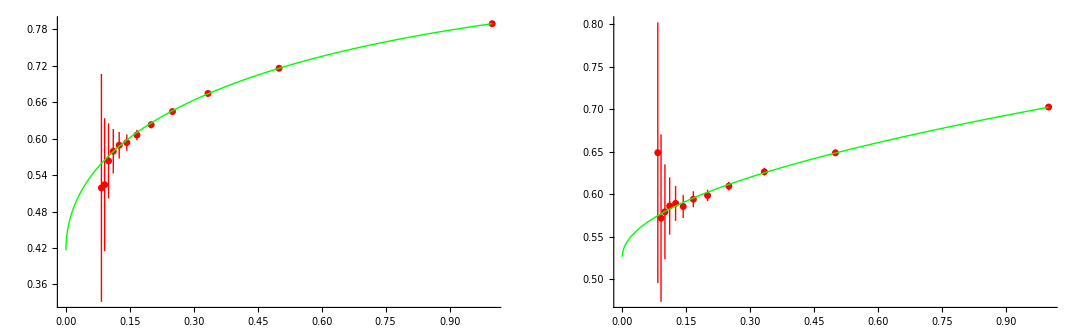

Mean link is 0.526548 +/- 0.0188188

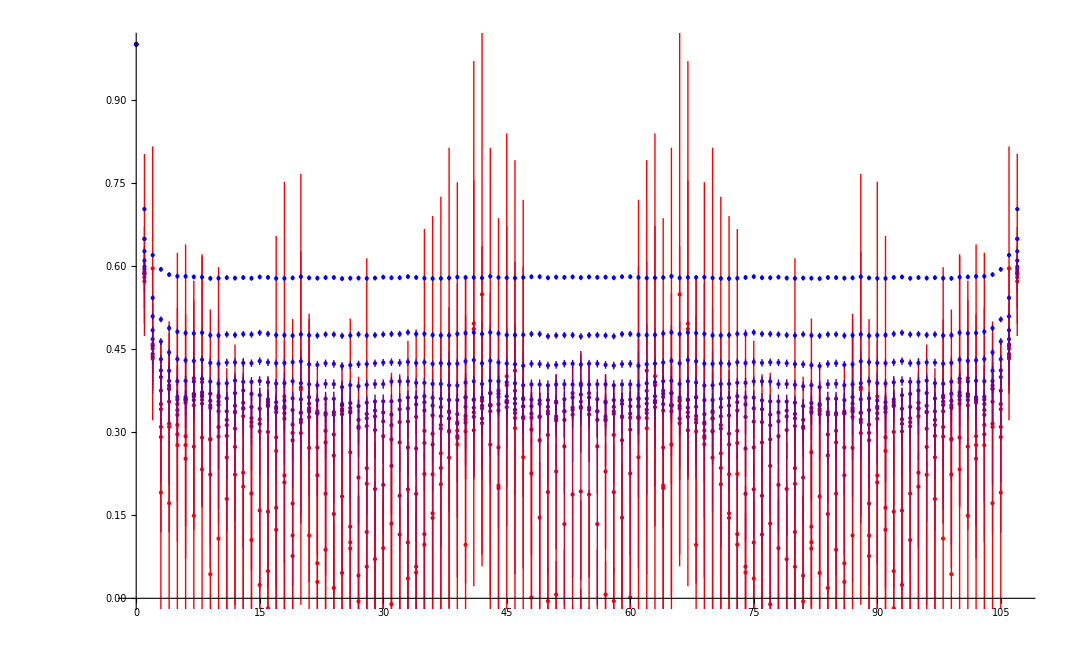

```mathematica
(* Unifying all the scripts *)
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Get["G:\\LAT\\sd_metropolis\\apps\\pcm_wc_mspace\\pcm_wc_mspace_tuning.m"];
(* Simulation parameters *)
λ=3.0120; LT=54; LS=108; mmax=11;
Suffix="d2_t"<>ToString[LT]<>"_s"<>ToString[LS]<>"_l"<>fsndig[λ,4];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
Print[ScalarFileName];
(* Importing the scalar data, obtaining the mean values and the correlation matrices *)
ScalarData=Import[ScalarFileName,"Table"];
np=Quotient[Length[ScalarData],mmax+1];
{GxMean,GxCorrelationMatrix}=XYCorrelatedDataStatistics[ScalarData,2,(mmax+1)];
{LinkMean,LinkCorrelationMatrix}=XYCorrelatedDataStatistics[ScalarData,4,(mmax+1)];
(* Now calculating the normalization factor basing on the first nontrivial order for Gx *) (* TODO: implement also leading order for the link and NL0 for link and Gx - to control the goodness *)
Gx0=GxOrder0[LT,LS,λ];
NFactor=(Gx0-1)/GxMean[[1]];
Print[np," data points, normalization factor is ",NFactor];
(* Rescale all the data properly *)
{GxMean,LinkMean}=1+NFactor {GxMean,LinkMean};
{GxCorrelationMatrix,LinkCorrelationMatrix}*=NFactor^2;
(* Fitting and extrapolating *)
xs=Table[1/(m+1),{m,0,mmax}];
Clear[x];
FitFuncs={1,√x,x};
{GxExtrapolation,GxExtrapolationCovariance}=FitCorrelatedData[xs,GxMean,GxCorrelationMatrix,FitFuncs,x];
{LinkExtrapolation,LinkExtrapolationCovariance}=FitCorrelatedData[xs,LinkMean,LinkCorrelationMatrix,FitFuncs,x];
(* Plots for the scalar data *)
GrGxData=PlotWithErrors[xs,GxMean,Sqrt[Diagonal[GxCorrelationMatrix]],PlotRange->{{0.0,All},{0.0,All}},PlotStyle->{Red,PointSize[0.01]}];
GrLinkData=PlotWithErrors[xs,LinkMean,Sqrt[Diagonal[LinkCorrelationMatrix]],PlotRange->{{0.0,All},{0.0,All}},PlotStyle->{Red,PointSize[0.01]}];
Clear[x];
GrGxExtrapolation=Plot[Sum[GxExtrapolation[[i]]FitFuncs[[i]],{i,1,Length[FitFuncs]}],{x,0,1},PlotRange->All,PlotStyle->{Green}];
GrLinkExtrapolation=Plot[Sum[LinkExtrapolation[[i]]FitFuncs[[i]],{i,1,Length[FitFuncs]}],{x,0,1},PlotRange->All,PlotStyle->{Green}];
GraphicsGrid[{{Show[GrGxData,GrGxExtrapolation,ImageSize->500],Show[GrLinkData,GrLinkExtrapolation,ImageSize->500]}}]
Print["Mean link is ",LinkExtrapolation[[1]]," +/- ",√LinkExtrapolationCovariance[[1,1]] ];
(* Importing the correlators *)
xs=Table[x,{x,0,LS-1}];
GrS={};
For[m=0,m≤mmax,m++,
r=m/mmax;
GxyDataFile="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\Gxy_"<>Suffix<>"_o"<>ToString[m]<>".dat";
(*Print[GxyDataFile];*)
GxyData=Import[GxyDataFile,"Real32"];
GxyData=Partition[GxyData,LS];
np1=Length[GxyData];
If[np1≠np,Print[Style["The number of data points in the correlator do not match the number of data points in scalars ",FontColor->Red],np1," ",np];];
{aGxy,dGxy}=1/np1 Sum[
cGxy=Re[Fourier[GxyData[[ip]],FourierParameters->{1,1}]];
{cGxy,cGxy^2}
,{ip,1,Length[GxyData]}];
dGxy=√((dGxy-aGxy^2)/(np1-1));
aGxy=1 + NFactor aGxy;
dGxy = NFactor dGxy;
AppendTo[GrS,PlotWithErrors[xs,aGxy,dGxy,PlotStyle->{RGBColor[r,0,1-r]},PlotRange->{0.0,1.0}]];
];
Show[Reverse[GrS]]
```

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
(* Set of lattice parameters *)
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
SourceNorms={0.0, 0.2540498,0.0,0.0,0.0,0.2733377};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
IncData={True,True,True,True,True,True};
(* Forming lists and plotting *)
GxPlots={}; mlPlots={};
For[iλ=1,iλ≤Length[lambdas],iλ++,
λ=lambdas[[iλ]];
SourceNorm = SourceNorms[[iλ]];
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
(* Generating file names *)

If[FileExistsQ[ScalarFileName],
Print["λ = ",λ,", ",ScalarFileName];
GxData=GetConvergenceData[ScalarFileName,1,2,1,1.0,12];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1.0,12];
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
NFactor=(1-O0data[[iλ]])/(1-MeanLinkData[[1,2]]);
GxData=LinearTransformColumn[GxData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,3,0.0,NFactor];
Print["NFactor = ",NFactor];
Gr2=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Gr3=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],PlotLabel->"<link>",DisplayFunction->$DisplayFunction];
GrUnFiltered=Show[Gr3,ImageSize->800];
Print[GrUnFiltered];
];
];
```

```mathematica
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/scalars*.dat  /g/LAT/sd_metropolis/data/pcm_wc_mspace/"];
Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/metropolis_stat*.dat  /g/LAT/sd_metropolis/data/pcm_wc_mspace/"];
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
iλ=6;
λ=lambdas[[iλ]]; 
c=(iλ-1)/(Length[lambdas]-1);
Color1=RGBColor[c,0,1-c];
Color2=RGBColor[0.7+0.3c,0.7,0.7+0.3(1-c)];
Print["λ = ",λ];
Do[
(*Manipulate[*)
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
McStatFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\metropolis_stat_"<>Suffix<>".dat";
If[FileExistsQ[ScalarFileName] && FileExistsQ[McStatFileName] ,
(* Analyzing the data *)
GxData=GetConvergenceData[ScalarFileName,1,2,1,1.0,13];
MeanLinkData=GetConvergenceData[ScalarFileName,1,4,1,1.0,13];
NFactor=(1-O0data[[iλ]])/(1-MeanLinkData[[1,2]]);
GxData=LinearTransformColumn[GxData,2,1-NFactor,NFactor];
GxData=LinearTransformColumn[GxData,3,0.0,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,2,1-NFactor,NFactor];
MeanLinkData=LinearTransformColumn[MeanLinkData,3,0.0,NFactor];
(* Fitting the data *)
MeanLinkDataToFit=Transpose[MeanLinkData];
FitWeights=MeanLinkDataToFit[[3]];
MeanLinkDataToFit=Transpose[Take[MeanLinkDataToFit,2]];
NMF=NonlinearModelFit[MeanLinkDataToFit,AA+BB x Log[x] +CC  x,{AA,BB,CC},x,Weights->1/FitWeights^2];
MeanLinkFit=NMF["BestFitParameters"];
Print[NMF["ParameterConfidenceIntervals"]];
GxDataToFit=Transpose[GxData];
FitWeights=GxDataToFit[[3]];
GxDataToFit=Transpose[Take[GxDataToFit,2]];
NMF=NonlinearModelFit[GxDataToFit,AA x Log[x]+ BB x Log[x]^2 +CC  x,{AA,BB,CC},x,Weights->1/FitWeights^2];
GxFit=NMF["BestFitParameters"];
Print[NMF["ParameterConfidenceIntervals"]];
(* Plotting *)
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
Gr2=Show[PlotWithErrors[GxData,Color1],PlotLabel->"<Gx>"];
GrGxFit=Plot[(AA x Log[x] +BB x Log[x]^2 +CC  x)/.GxFit,{x,0.001,1.0},PlotStyle->{Green},PlotRange->All];
GrExact=ListPlot[MeanLinkExactData,PlotStyle->{Color2,PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
GrMeanLinkFit=Plot[(AA+BB x Log[x] +CC  x)/.MeanLinkFit,{x,0.001,1.0},PlotStyle->{Green},PlotRange->All];
Gr3=Show[GrExact,PlotWithErrors[MeanLinkData,Color1],GrMeanLinkFit,PlotLabel->"<link>"];
Print[GraphicsGrid[{{Show[Gr2,GrGxFit],Gr3}},ImageSize->1000]];
(* Analyzing the algorithm performance *)
McStatData=Transpose[Import[McStatFileName,"Table"]];
Print[Length[McStatData[[1]]]," points"];
PrintStatistics[McStatData[[1]],"Acceptance Rate"];
PrintStatistics[McStatData[[9]],"Mean return time"];
Print["#################################################################################################################"];
];
,{a,{0.5,1.0,1.5}},{cc,{0.5,1.0,1.5}},{NN,{0.5,1.0,1.5}}
];
```

```mathematica
(* Fitting taking into account the covariance matrix *)
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
lambdas={5.0, 4.0, 3.57, 3.45, 3.33, 3.23};
VRdata={0.781, 0.708, 0.6499, 0.62134, 0.56809, 0.51202};
O0data={0.5577,0.6270,0.6590,0.66821,0.6775,0.6853};
O1data={0.4541,0.5464,0.5888,0.6009,0.6131,0.6234};
iλ=6;
λ=lambdas[[iλ]]; 
MeanLinkExactData={{0.0,1-VRdata[[iλ]]},{0.5,O1data[[iλ]]},{1.0,O0data[[iλ]]}};
mmax=12;
a=1.0; cc=1.0; NN = 1.0;
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
ScalarFileName="G:\\LAT\\sd_metropolis\\data\\pcm_wc_mspace\\scalars_"<>Suffix<>".dat";
ScalarData=Import[ScalarFileName,"Table"];
LinkAverage=Table[0.0,{m,1,mmax}];
LinkCorrelation=Table[0.0,{m1,1,mmax},{m2,1,mmax}];
DataCounter=0;
For[i=1,i≤Length[ScalarData],i+=mmax,
For[m1=1,m1≤mmax,m1++,
mcheck=ScalarData[[i+m1-1,1]]+1;
If[mcheck≠m1,Print["Alarma!!!"];];
LinkAverage[[m1]]+=ScalarData[[i+m1-1,4]];
For[m2=1,m2≤mmax,m2++,
LinkCorrelation[[m1,m2]]+=ScalarData[[i+m1-1,4]] ScalarData[[i+m2-1,4]];
];
];
DataCounter++;
];
LinkAverage /= DataCounter;
LinkCorrelation=LinkCorrelation/DataCounter - KroneckerProduct[LinkAverage,LinkAverage];
NFactor=(O0data[[iλ]]-1)/LinkAverage[[1]];
Print["NFactor = ",NFactor];
LinkAverage=1+NFactor LinkAverage;
LinkCorrelation*=NFactor^2;
(* Table of conventional errors *)
LinkErrors=Table[√(LinkCorrelation[[m,m]]/(DataCounter-1)),{m,1,mmax}];
(* Defining chi2 for fitting *)
Clear[x]; 
FitFuncs={1,√x,x};(*{1,x Log[x], x, x Log[x]^2};*)
parlist=Table[Symbol["p"<>ToString[i]],{i,1,Length[FitFuncs]}];
F[x_]:=Sum[parlist[[i]] FitFuncs[[i]],{i,1,Length[FitFuncs]}];
LCI=Inverse[LinkCorrelation];
Chi2[pars_]:=Module[{Y0,m,i},
Y0=Table[Sum[(pars[[i]] FitFuncs[[i]])/.{x->1/m},{i,1,Length[FitFuncs]}],{m,1,mmax}];
0.5/(DataCounter-1)(LinkAverage-Y0).LCI.(LinkAverage-Y0)
];
Print[LinkAverage];
Print[MatrixForm[LinkCorrelation]," ",Eigenvalues[LinkCorrelation]];
FitVals=NMinimize[Chi2[parlist],parlist][[2]];
Print[FitVals];
(* Getting the parameter Jacobian *)
P2=(DataCounter-1) Table[Sum[(FitFuncs[[i]]/.{x->1/m1})LCI[[m1,m2]] (FitFuncs[[j]]/.{x->1/m2}),{m1,1,mmax},{m2,1,mmax}],{i,1,Length[FitFuncs]},{j,1,Length[FitFuncs]}];
P2=Inverse[P2];
Print[MatrixForm[P2]];
Print["Mean plaquette is between ",(p1/.FitVals )- √P2[[1,1]]," and ",(p1/.FitVals) + √P2[[1,1]]," (", 100.0 √P2[[1,1]]/(p1/.FitVals)," %)"];
(* Plotting *)
LinkAverageToPlot=Transpose[{Table[1/m,{m,1,mmax}],LinkAverage,LinkErrors}];
Gr1=PlotWithErrors[LinkAverageToPlot,Red];
Gr2=ListPlot[MeanLinkExactData,PlotStyle->{RGBColor[1.0,0.7,0.7],PointSize[0.02]},PlotRange->{{0.0,All},{0.0,All}}];
Gr3=Plot[F[x]/.FitVals,{x,0.001,1.0},PlotStyle->{Green}];
Show[Gr2,Gr3,Gr1]
```

```mathematica
(* Looking at the full correlators *)
$HistoryLength=0;
Get["G:\\LAT\\sd_metropolis\\convergence_analysis.m"];
mmax=12; λ=3.23;LS=32; NFactor=12189.0;
a=1.0; cc=1.0; NN = 1.0;
Print["a = ",a,", cc = ",cc,", NN = ",NN];
Suffix="d2_t32_s32_l"<>fsndig[λ,4]<>"_a"<>fsndig[a,2]<>"_c"<>fsndig[cc,2]<>"_n"<>fsndig[NN,2];
Run["ssh-pageant rsync -v -z di72kov@lxlogin5.lrz.de:/home/hpc/b3101/di72kov/sd_metropolis/data/pcm_wc_mspace/Gxy_"<>Suffix<>"_o*.dat /c/DATA/pcm_wc_mspace_raw_data/"];
GrS={};
MidPoints={};
For[m=1,m≤mmax,m++,
r=(m-1)/(mmax-1);
GxyDataFile="C:\\DATA\\pcm_wc_mspace_raw_data\\Gxy_"<>Suffix<>"_o"<>ToString[m-1]<>".dat";
Print[GxyDataFile];
GxyData=Import[GxyDataFile,"Table"];
aGxy=Table[0.0,{x,1,LS}];
dGxy=Table[0.0,{x,1,LS}];
DataCounter=0;
For[i=1,i≤Length[GxyData],i+=LS,
mGxy=Table[GxyData[[i+p,2]],{p,0,LS-1}];
cGxy=Re[Fourier[mGxy,FourierParameters->{1,1}]];
aGxy+=cGxy;
dGxy+=cGxy^2;
DataCounter++;
];
aGxy/=DataCounter; dGxy =√((dGxy/DataCounter - aGxy^2)/(DataCounter-1));
GxyToPlot=Transpose[{Table[x,{x,0,LS-1}],1+NFactor aGxy,NFactor dGxy}];
AppendTo[MidPoints,{1/m,1+NFactor aGxy[[LS/2+1]],NFactor dGxy[[LS/2+1]]}];
Gr1=PlotWithErrors[GxyToPlot,RGBColor[r,0,1-r]];
(*Print[Show[Gr1]];*)
AppendTo[GrS,Gr1];
];
Show[GrS]
PlotWithErrors[MidPoints,Green]
```

```mathematica
Fourier[{1,0,0,0,0},FourierParameters->{1,1}]
```

```mathematica
x=1; y=2;
{x,y}=1 + 2 {x, y};
Print[{x, y}];
```

```mathematica
Partition[{1,2,3,4,5,6},3]
```

{{1,2,3},{4,5,6}}